# Map(/@)

#### applies f to each element on certain level

```mathematica
Map[f,{a,b,c,d,e}]
```

{f[a],f[b],f[c],f[d],f[e]}

```mathematica
f/@{a,b,c,d}
```

{f[a],f[b],f[c],f[d]}

```mathematica
(1+g[#])&/@{a,b,c,d,e}
```

{1+g[a],1+g[b],1+g[c],1+g[d],1+g[e]}

```mathematica
Function[x,x^2]/@{1,10,100}
```

{1,100,10000}

```mathematica
Map[f,{{a,b},{c,d,e}}]
```

{f[{a,b}],f[{c,d,e}]}

```mathematica
Map[f,{{a,b},{c,d,e}},{2}]
```

{{f[a],f[b]},{f[c],f[d],f[e]}}

```mathematica
Map[f][{a,b,c,d}]
```

{f[a],f[b],f[c],f[d]}

```mathematica
Map[h,<|a-> b,c-> d|>]
```

<|a→h[b],c→h[d]|>

```mathematica
Map[h,<|a-> <|b-> c|>, d-> <|e-> f|>|>,{2}]
```

<|a→<|b→h[c]|>,d→<|e→h[f]|>|>

```mathematica
If[PrimeQ[#],Framed[#],#]& /@ Range[50]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

# MapThread

Apply f to corresponding pairs of elements:

```mathematica
MapThread[f,{{a,b,c},{1,2,3}}]
```

{f[a,1],f[b,2],f[c,3]}

Apply f to elements of a matrix:

```mathematica
MapThread[f,{{{a,b},{c,d}},{{1,2},{3,4}}}]
```

{f[{a,b},{1,2}],f[{c,d},{3,4}]}

# MapIndexed

# Map a Function over a list

# MapAll

# Append

```mathematica
Append[{a,b,c,d},x]
```

{a,b,c,d,x}

```mathematica
Append[{{a,b},{c,d}},{x,y}]//MatrixForm
```

(a | b
c | d
x | y)

```mathematica
Map[Append[#,x]&, {{a,b},{c,d}}]//MatrixForm
```

(a | b | x
c | d | x)

```mathematica
MapThread[Append,{{{a,b},{c,d}},{x,y}}]//MatrixForm
```

(a | b | x
c | d | y)

```mathematica
Append[{a,b,c},{x,y}];
Flatten[%]
```

{a,b,c,x,y}

# Flatten

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}}]
```

{a,b,c,d,e,f,g,h}

# Table

```mathematica
Table[i^2,{i,1,10,2}]
```

{1,9,25,49,81}

```mathematica
Table[10i+j,{i,4},{j,3}]//MatrixForm
```

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33
41 | 42 | 43)

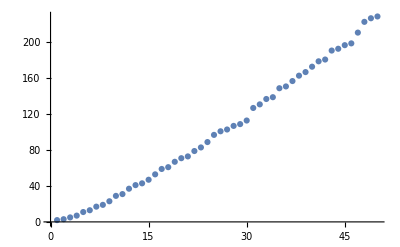

```mathematica
ListPlot[Table[Prime[i],{i,50}]]
```

```mathematica
Table[Style["Pan",s],{s,10,100,25}]
```

{Pan,Pan,Pan,Pan}